Lecture Intro AceFEM
Notebook for Exercises 
Created by Michele Marino, Department of Civil Engineering and Computer Science, University of Rome Tor Vergata, Italy
Date: 02 November 2021 - Contact: m.marino@ing.uniroma2.it

# Element Codes

## T1LE - Linear elasticity

### Initialization

```mathematica
<<AceGen`;
SMSInitialize["T1LE","Environment"-> "AceFEM","Mode"-> "Optimal"];
SMSTemplate["SMSTopology"->"T1",
(*Numerical Integration*) "SMSDefaultIntegrationCode"->35,
(*35 -Graphics-*)
(*Initialize domain data for material parameters*)
"SMSDomainDataNames"-> {"E -Young","ν -Poisson"}, "SMSDefaultData" -> {1,0.49},
(*Expected symmetry in tangent stiffness*)
"SMSSymmetricTangent"->True,
"SMSNoElementData" -> 3];

RelevantNumbers[]:=(
nen=SMSNoNodes; 
ndim=SMSNoDimensions; 
ndof=SMSNoDOFGlobal;
nip=SMSIO["No. integration points"];
(* Equivalent to: SMSInteger[es$$["id", "NoIntPoints"]] *)
)
```

### Element definitions

```mathematica
ElementDefinitions[Ig_]:=(
(*MATERIAL AND ELEMENT DATA*)
{Ee,ν}⊨SMSIO["Domain data"];

{ξ,η,ζ}⊨SMSIO["Integration point"[Ig]];
wgp⊨SMSIO["Integration weight"[Ig]];

{𝕏IO,𝕦IO}⊨SMSIO["All coordinates and DOFs"];
𝕦e=Flatten[𝕦IO];

(*SHAPE FUNCTIONS*)
N1⊨1-ξ-η;
N2⊨ξ;
N3⊨η;
ℕh⊨{N1, N2, N3};

(*ISOPARAMETRIC MAPPING*)
𝕏⊨SMSFreeze[ℕh.𝕏IO];
𝕁e⊨SMSD[𝕏,{ξ,η}]; 
Jed⊨SMSDet[𝕁e];

(*KINEMATICS AND CONSTITUTIVE BEHAVIOUR*)
𝕦⊨ℕh.𝕦IO;
ℍ2D⊨SMSD[𝕦,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
ℍ⊨{{ℍ2D⟦1,1⟧,ℍ2D⟦1,2⟧,0},{ℍ2D⟦2,1⟧,ℍ2D⟦2,2⟧,0},{0,0,0}};
SMSFreeze[𝔻,(ℍ+Transpose[ℍ])/2,"Symmetric"-> True];
{λ,μ}⊢SMSHookeToLame[Ee,ν];
Ψe⊨ λ/2 Tr[𝔻]^2+μ Tr[𝔻.𝔻];
)
```

### Tangent and Residual

```mathematica
SMSStandardModule["Tangent and residual"];
RelevantNumbers[];

SMSDo[Ig,1,nip];

ElementDefinitions[Ig];

SMSDo[
Rgi⊨Jed wgp SMSD[Ψe,𝕦e,i];
SMSIO[Rgi,"Add to","Residual"[i]];
SMSDo[
Kgij⊨ SMSD[Rgi,𝕦e,j];
SMSIO[Kgij,"Add to","Tangent"[i,j]];
,{j,i,ndof}];
,{i,1,ndof}];
SMSEndDo[];
```

### Post-processing

```mathematica
SMSStandardModule["Postprocessing"];
RelevantNumbers[];

(* Initial creation on aleatory multivalue variables: total forces *)
SMSM[Fxx, 0];
SMSM[Fyy, 0];
SMSM[Fxy,0];


SMSDo[Ig,1,nip, 1, {Fxx, Fyy, Fxy} ];

ElementDefinitions[Ig];
σ⊨SMSD[Ψe,𝔻,"Symmetric"->True];

(* Creazione di nuove istanze dalle precedentemente create variabili ausiliarie *) 
SMSS[Fxx, Fxx + Jed wgp σ⟦1, 1⟧];
SMSS[Fyy, Fyy + Jed wgp σ⟦2, 2⟧];
SMSS[Fxy, Fxy + Jed wgp σ⟦1, 2⟧];


SMSIO[
{"Dxx"->𝔻⟦1,1⟧,"Dxy"->𝔻⟦1,2⟧,"Dyy"->𝔻⟦2,2⟧,"σxx"->σ⟦1,1⟧,"σxy"->σ⟦1,2⟧,"σyy"->σ⟦2,2⟧}
,"Export to","Integration point post"[Ig]]

SMSEndDo[{Fxx, Fyy, Fxy}];

SMSR[Ftxx, Fxx];
SMSR[Ftyy, Fyy];
SMSR[Ftxy, Fxy];

(* Esportazione dei 3 dati d'interesse per l'elemento come vettore riga*) 
SMSExport[{Ftxx, Ftyy, Ftxy}, Table[ed$$["Data", i], {i, 1, SMSNoElementData}]];
𝕦h⊨Transpose[𝕦IO];
SMSIO[{"DeformedMeshX"->𝕦h⟦1⟧,"DeformedMeshY"->𝕦h⟦2⟧,"u"->𝕦h⟦1⟧,"v"->𝕦h⟦2⟧},"Export to","Nodal point post"];
(*SMTElementData[element number, "Data"]
ed$$["Data",i]*)
```

### Code generation

```mathematica
SMSWrite[];
```

File: T1LE.c  Size: 7941  Time: 1
Method | SKR | SPP
No.Formulae | 47 | 37
No.Leafs | 781 | 633

# FEM Simulations

## Trabecular bone

```mathematica
<<AceGen`;
<<AceFEM`;
```

### Useful function

function Useful

```mathematica
PoreDistribution[Nincl_,diameter_,distribData_]:=(
radius=diameter/2;
distribData1=100*distribData/Total[distribData];
distribution=EmpiricalDistribution[distribData1->radius];
Print[DiscretePlot[PDF[distribution,x],{x,0,1000},Joined->True]];
Export[StringJoin[NotebookDirectory[],"distr.pdf"],DiscretePlot[PDF[distribution,x],{x,0,1000},Joined->True]];
Rcvec=RandomVariate[distribution,Nincl];
Return[N[Rcvec/1000,2]]
);
```

```mathematica
(* parametri geoemtrici iniziali*)
meshing={0.00001};
meshingbound={0.001};
Nincl=300; 
diameter={200,300,400,600,700};
distribData={3.7, 3.2,2.5,2.7,2.5};
```

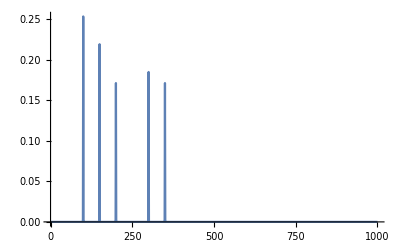

```mathematica
Rcvec=PoreDistribution[Nincl,diameter,distribData];
```

```mathematica
volfrac=0.6;
inctot=Nincl;
Ainc=Total[N[Pi*(Rcvec*Rcvec)]];
AT=Ainc /volfrac;
L=Sqrt[AT];
Print["Lato RVE:", L *1000," pixel"]
Counts[Rcvec*2]
Length[Rcvec]
Print[Rcvec];
```

Lato RVE:8999.31 pixel

<|0.6→60,0.3→59,0.4→51,0.2→82,0.7→48|>

300

{0.3,0.15,0.3,0.2,0.1,0.15,0.3,0.15,0.2,0.35,0.2,0.1,0.3,0.1,0.2,0.2,0.3,0.15,0.15,0.15,0.1,0.3,0.1,0.1,0.3,0.15,0.15,0.1,0.1,0.3,0.15,0.15,0.35,0.1,0.1,0.35,0.3,0.1,0.1,0.1,0.2,0.2,0.15,0.15,0.3,0.15,0.15,0.35,0.35,0.35,0.3,0.2,0.1,0.15,0.3,0.35,0.2,0.3,0.3,0.1,0.15,0.3,0.15,0.15,0.15,0.3,0.3,0.35,0.3,0.15,0.2,0.15,0.1,0.35,0.1,0.1,0.3,0.1,0.35,0.15,0.35,0.1,0.15,0.15,0.1,0.1,0.1,0.15,0.15,0.35,0.1,0.3,0.1,0.1,0.3,0.2,0.35,0.15,0.1,0.1,0.2,0.2,0.3,0.15,0.1,0.1,0.3,0.1,0.3,0.1,0.3,0.15,0.2,0.3,0.2,0.2,0.35,0.35,0.3,0.1,0.15,0.35,0.2,0.15,0.1,0.3,0.35,0.2,0.3,0.1,0.35,0.15,0.2,0.1,0.2,0.1,0.35,0.3,0.2,0.2,0.35,0.2,0.1,0.15,0.35,0.35,0.35,0.35,0.15,0.1,0.15,0.2,0.15,0.2,0.15,0.3,0.1,0.2,0.15,0.35,0.1,0.1,0.2,0.1,0.35,0.2,0.2,0.3,0.1,0.35,0.1,0.1,0.15,0.3,0.3,0.2,0.1,0.15,0.2,0.1,0.1,0.15,0.3,0.1,0.3,0.35,0.3,0.2,0.15,0.35,0.3,0.2,0.15,0.1,0.2,0.15,0.15,0.1,0.1,0.1,0.2,0.2,0.15,0.1,0.3,0.35,0.2,0.3,0.35,0.3,0.2,0.1,0.35,0.3,0.3,0.35,0.1,0.1,0.3,0.1,0.35,0.1,0.35,0.1,0.3,0.3,0.2,0.2,0.35,0.1,0.1,0.2,0.2,0.3,0.2,0.15,0.15,0.1,0.3,0.2,0.35,0.15,0.3,0.2,0.15,0.3,0.35,0.3,0.15,0.1,0.3,0.1,0.1,0.3,0.3,0.1,0.15,0.15,0.1,0.1,0.35,0.35,0.35,0.15,0.3,0.35,0.1,0.15,0.1,0.1,0.15,0.2,0.2,0.1,0.2,0.1,0.3,0.1,0.15,0.3,0.1,0.1,0.35,0.3,0.3,0.1,0.35,0.35,0.2,0.1,0.3,0.15,0.15,0.35,0.35,0.1,0.2,0.1,0.2,0.35}

```mathematica
Clear[center]
Clear[radi]
center=Import["centers.mat"];
center=Flatten[center,1];
center⟦1⟧
radi=Import["radii.mat"];
radi=Flatten[radi];
radi⟦1⟧
Length[center]
Length[radi]
```

{1.04,3.59}

0.1

300

300

```mathematica
Histogram[radi]
𝒟=EmpiricalDistribution[radi];
DiscretePlot[PDF[𝒟,x],{x,radi},PlotStyle->RGBColor[0.650,0.486,0.321],Joined->True]
Export[StringJoin[NotebookDirectory[],"distribution_300.pdf"],%]

var=N[diameter/2000];
```

C:\Users\bigba\OneDrive\Documenti\GitHub\bone-homogenization\FEM\pore_distribution2\mesh_300\distribution_300.pdf

```mathematica
Clear[center]
Clear[radi]
L=9.035;
Lx = L; 
Ly = L; 
(*
center=Import["centers.mat"];
center=Flatten[center,1];*)
center=Import["centers.mat"];
center=Flatten[center,1]

radi=Import["radii.mat"];
radi=Flatten[radi]
(*
Ωext=Rectangle[{0,0},{Lx,Ly}];
    Ω=Ωext;
*)


mark=Length[radi];

(*
Do[
  Ω=RegionDifference[  Ω,Disk[center⟦i⟧, {radi⟦i⟧,radi⟦i⟧}]];
,{i,1,mark}];
*)
condition=(x-center⟦1,1⟧)^2+(y-center⟦1,2⟧)^2>=radi⟦1⟧^2&&(x-center⟦2,1⟧)^2+(y-center⟦2,2⟧)^2>=radi⟦2⟧^2


Do[
 condition=And[condition,(x-center⟦i,1⟧)^2+(y-center⟦i,2⟧)^2>=radi⟦i⟧^2];
,{i,1,mark}];
condition;

 Ω=ImplicitRegion[condition,{{x,0,L},{y,0,L}}];
(*RegionPlot[Ω]*)
marker={{{Lx/100,Ly/100},1}};

Do[
marker=Join[marker,{{center⟦i⟧,2}}]
,{i,1,mark}];
(*
RegionPlot[Ω]
*)
(*
RegionBounds[Ω]
*)
mesh=ToElementMesh[Ω,{ {0,L},{0,L}},"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1,"MaxCellMeasure"->meshing,"MaxBoundaryCellMeasure"->meshingbound];

(*
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1,"MaxCellMeasure"->meshing,"MaxBoundaryCellMeasure"->meshingbound];*)
(*
im=-Graphics-;

dim=ImageDimensions[im]
Lx = dim⟦1⟧ 
Ly =dim⟦2⟧
mesha=ImageMesh[im]
mesh=ToElementMesh[mesha,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1];
*)
(*RegionPlot[Ω]*)
(*mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1,"MaxCellMeasure"->meshing,"MaxBoundaryCellMeasure"->meshingbound];*)
(*mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1];*)
(*
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1,"MaxCellMeasure"->meshing,"MaxBoundaryCellMeasure"->meshingbound];
(*mesh=ToElementMesh[Ωext,"MeshOrder"->1,"RegionMarker"->{{{Lx/100,Ly/100},1}},"MeshElementType"->TriangleElement,"MaxCellMeasure"->0.01];
*)
mesh=ToElementMesh[Ω,"RegionHoles"->None,"RegionMarker"->marker,"MeshOrder"->1];*)
%["Wireframe"["MeshElement"->"BoundaryElements"]]
(*%["Wireframe"]*)
```

{{1.04,3.59},{2.53,1.5},{5.17,2.22},{6.78,5.41},{1.92,2.41},{3.39,4.92},{6.89,7.95},{6.72,2.58},{0.91,0.14},{2.24,1.56},{6.53,3.98},{5.86,4.37},{4.33,2.99},{6.98,6.65},{7.93,6.91},{8.16,0.18},{0.92,5.6},{2.31,8.82},{5.2,1.24},{4.37,6.5},{1.55,0.87},{7.43,7.25},{4.16,6.3},{5.61,4.27},{7.78,0.72},{2.79,5.62},{8.11,2.72},{4.18,0.15},{7.3,0.16},{1.67,6.77},{0.82,2.16},{7.27,4.44},{1.14,0.25},{6.62,0.84},{8.48,2.31},{5.03,5.82},{0.26,4.82},{6.12,8.13},{5.89,0.15},{1.31,5.02},{2.59,2.27},{4.49,1.46},{6.24,0.21},{4.27,7.18},{1.52,1.82},{2.28,5.14},{3.13,0.28},{2.92,2.8},{3.15,7.53},{5.06,8.02},{4.93,0.86},{8.9,6.61},{7.19,0.48},{2.51,3.29},{8.47,7.79},{4.26,1.75},{3.43,0.15},{4.93,6.37},{7.68,7.14},{5.02,7.28},{6.39,7.35},{7.86,5.32},{7.81,2.65},{7.47,6.1},{7.84,7.81},{7.95,4.3},{1.51,6.09},{4.7,1.98},{2.,5.15},{1.7,3.99},{3.87,4.07},{6.14,1.23},{5.92,6.23},{4.36,5.11},{8.52,7.15},{6.91,2.9},{0.17,0.98},{6.15,5.89},{1.31,1.63},{4.16,7.77},{0.31,8.72},{0.91,2.86},{2.44,3.69},{4.18,7.43},{1.18,1.95},{4.44,2.1},{1.67,5.85},{4.26,5.65},{5.63,1.9},{5.66,0.92},{1.47,0.15},{2.65,5.85},{2.89,0.91},{6.15,1.52},{2.8,8.71},{3.,5.95},{6.87,0.77},{1.95,7.38},{3.57,8.02},{8.77,6.34},{6.64,2.97},{7.6,3.59},{4.41,3.97},{4.96,4.67},{6.88,7.66},{8.72,1.09},{4.78,3.3},{6.87,3.86},{1.92,6.83},{3.59,7.08},{1.43,3.38},{3.97,8.77},{3.69,8.67},{8.24,2.94},{8.57,4.79},{6.66,3.67},{8.28,4.84},{0.31,5.45},{0.96,3.99},{5.27,5.32},{8.79,0.46},{8.82,0.77},{5.09,6.14},{7.88,3.53},{2.18,6.67},{2.15,4.82},{2.35,4.07},{2.6,3.97},{7.11,1.37},{5.73,3.04},{0.21,3.11},{4.86,4.94},{8.78,3.86},{7.07,4.12},{4.22,4.22},{6.87,5.05},{1.84,2.76},{2.27,4.37},{1.16,8.77},{0.31,7.92},{8.63,7.53},{3.04,4.97},{1.72,2.08},{0.27,1.42},{1.34,0.5},{6.01,3.25},{1.11,4.72},{1.31,3.99},{6.09,4.6},{0.26,6.4},{1.95,8.77},{6.48,5.67},{8.78,2.12},{6.52,3.29},{4.67,1.06},{2.03,4.07},{7.19,4.79},{0.46,1.13},{1.16,4.31},{2.65,5.3},{3.5,4.02},{3.15,4.67},{2.72,1.82},{0.26,1.82},{8.07,3.85},{5.72,3.38},{5.01,3.59},{3.65,1.16},{1.16,6.},{8.67,5.91},{1.19,3.13},{1.67,5.11},{4.64,2.94},{7.15,5.96},{0.77,3.17},{3.63,2.17},{7.81,0.2},{1.52,3.02},{7.58,0.4},{0.47,2.96},{0.96,7.13},{6.12,4.21},{3.22,7.82},{8.57,0.2},{5.23,0.95},{8.09,8.03},{1.51,7.23},{4.17,2.51},{7.73,3.09},{5.71,1.37},{6.14,6.83},{4.46,4.67},{5.45,6.47},{3.57,2.78},{4.15,1.16},{5.59,2.42},{0.83,1.7},{5.48,3.82},{5.59,8.68},{3.75,1.68},{6.45,7.8},{1.37,5.51},{6.96,8.39},{2.7,7.67},{3.92,5.26},{0.61,7.48},{2.3,7.13},{8.06,2.24},{7.56,4.05},{4.86,4.19},{3.92,5.92},{0.52,6.83},{4.79,2.46},{3.33,0.7},{3.74,3.43},{2.67,0.4},{6.19,3.73},{4.39,3.52},{3.95,0.51},{6.05,1.95},{8.62,2.7},{2.37,1.06},{2.21,2.01},{1.93,6.3},{6.73,0.35},{1.21,7.8},{0.47,3.58},{3.,4.19},{2.57,4.76},{6.27,8.57},{4.58,6.09},{8.46,1.69},{2.,7.8},{4.81,8.57},{4.76,6.85},{7.74,4.79},{2.18,5.65},{3.08,1.38},{7.35,7.76},{5.1,1.73},{4.67,7.67},{1.21,6.57},{0.42,2.41},{1.02,0.97},{7.3,2.5},{7.32,5.42},{5.48,4.83},{6.68,6.25},{6.12,0.71},{8.57,5.28},{3.05,3.34},{8.43,3.41},{5.21,3.06},{0.72,8.32},{7.69,8.47},{6.22,2.68},{8.03,5.89},{4.76,5.4},{1.97,3.38},{8.44,4.3},{3.09,2.27},{3.97,6.76},{5.41,0.41},{6.13,5.15},{1.57,8.37},{5.59,7.97},{1.95,0.47},{8.32,6.62},{1.7,4.54},{8.03,1.29},{8.57,8.55},{5.53,7.24},{6.61,1.33},{6.85,7.14},{7.37,0.97},{3.29,5.52},{2.39,2.76},{2.44,8.32},{3.69,7.55},{4.09,8.25},{2.65,6.42},{3.39,6.3},{8.1,7.4},{0.72,5.11},{0.57,4.37},{3.1,7.05},{7.44,1.74},{3.22,8.37},{0.47,0.45},{7.09,3.37},{4.64,0.41},{6.7,2.06},{3.74,4.54},{1.74,1.34},{1.3,2.47},{0.57,5.95},{6.65,4.5},{7.49,6.62},{5.56,5.74},{8.28,0.72}}

{0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.3,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35,0.35}

(-1.04+x)^2+(-3.59+y)^2≥0.01&&(-2.53+x)^2+(-1.5+y)^2≥0.01

```mathematica
VoigtReussTest[verbOutput_,ℚ_,materialProp_,volfrac_]:=(
Emat1=materialProp⟦1,1⟧;
νmat1=materialProp⟦1,2⟧;
Emat2=materialProp⟦2,1⟧;
νmat2=materialProp⟦2,1⟧;
𝕊calc[mater_]:=(
𝕊materiale=DiagonalMatrix[{1/mater⟦1⟧,1/mater⟦1⟧,1/mater⟦1⟧,2(1+mater⟦2⟧)/mater⟦1⟧,2(1+mater⟦2⟧)/mater⟦1⟧,2(1+mater⟦2⟧)/mater⟦1⟧}];
𝕊materiale⟦1,2⟧=-(mater⟦2⟧/mater⟦1⟧);𝕊materiale⟦1,3⟧=-(mater⟦2⟧/mater⟦1⟧);
𝕊materiale⟦2,1⟧=-(mater⟦2⟧/mater⟦1⟧);𝕊materiale⟦2,3⟧=-(mater⟦2⟧/mater⟦1⟧);
𝕊materiale⟦3,1⟧=-(mater⟦2⟧/mater⟦1⟧);𝕊materiale⟦3,2⟧=-(mater⟦2⟧/mater⟦1⟧);
Return[𝕊materiale];
);
𝕊rid[𝕊𝕊_]:=(
Sridotta=DiagonalMatrix[{0,0,0}];
Do[
Sridotta⟦i,j⟧=𝕊𝕊⟦i,j⟧,{i,1,2},{j,1,2}];
Sridotta⟦3,3⟧=𝕊𝕊⟦6,6⟧;
Return[Sridotta];
);
fracweigth[M1_,M2_,frac_]:=(
M=M1*(1-frac)+M2*frac;
Return[M]
);

𝕊materiale1=𝕊calc[{Emat1,νmat1}];
ℂmateriale1=Inverse[𝕊materiale1];
𝕊materiale2=𝕊calc[{Emat2,νmat2}];
ℂmateriale2=Inverse[𝕊materiale2];
𝕊mat1=𝕊rid[𝕊materiale1];
𝕊mat2=𝕊rid[𝕊materiale2];
ℂmat1=𝕊rid[ℂmateriale1];
ℂmat2=𝕊rid[ℂmateriale2];
ℂvoigt=fracweigth[ℂmateriale1,ℂmateriale2,volfrac];
𝕊reuss=fracweigth[𝕊materiale1,𝕊materiale2,volfrac];

ℂreuss=Inverse[𝕊reuss];
ℂvoigt=𝕊rid[ℂvoigt];
ℂreuss=𝕊rid[ℂreuss];

;
CLiminf=ℚ-ℂreuss;
CLimsup=ℂvoigt - ℚ;
check1=PositiveDefiniteMatrixQ[CLiminf];
check2=PositiveDefiniteMatrixQ[CLimsup];
If[And[check1,check2],StylePrint["Reuss and Voigt lim is verified",FontColor->Green],StylePrint["Lim not verified",FontColor->Red]];
If[Not[check1],Print["Reuss failed"]];
If[Not[check2],Print["Voigt failed"]];

If[verbOutput, 
Print["𝕔mat1: ",N[MatrixForm[ℂmat1]],"  ","𝕤mat1: ",N[MatrixForm[𝕊mat1]]];
Print["𝕔mat2: ",N[MatrixForm[ℂmat2]],"  ","𝕤mat2 : ",N[MatrixForm[𝕊mat2]]];
Print[Subscript["𝕔","Voigt"],": ",MatrixForm[ℂvoigt]];
Print[Subscript["𝕔","Reuss"],": ",MatrixForm[ℂreuss]];
];
StylePrint["",FontColor->Black];
);

Checkconvergence[meshprop_,meshingbound_,verboseOutput_,DebugVal_,iteration_]:=(
testBC={{1,0,0},{0,0,1},{0,0.5,0}}; (*non sono le ϵ ma valori di comodo per i parametri a,b,c per le BC tipo essenziale*)
ℂcol={{0,0,0},{0,0,0},{0,0,0}};
materialprop={{5000,0.3},{0.15,0.1}}; (* E, ν material *)
(*
Emat1=5000;
νmat1=0.3;*)

(*
Emat2=0.15;
νmat2=0.1;
*)
Do[
ℂcol⟦i⟧=TEST[testBC⟦i⟧,meshprop,meshingbound,materialprop];
,{i,1,3}]
ℂcol;
ℚ=Transpose[ℂcol];
Print[Subscript["ℂ",StringJoin["om",ToString[iteration]]],": ",MatrixForm[ℚ]];
Export[StringJoin[NotebookDirectory[],"C_om_",ToString[iteration],".tex"],MatrixForm[ℚ]];

If[DebugVal,(* set it to true only IF TESTING ISOTROPIC MATERIAL !!!!*)
solved1=SolveValues[E1*(1-ν12)/((1 -2*ν12)(1+ν12))==ℚ⟦1,1⟧&&E1*ν12/((1 -2*ν12)(1+ν12))==ℚ⟦1,2⟧,{E1,ν12}];
solved2=SolveValues[E2*(1-ν21)/((1 -2*ν21)(1+ν21))==ℚ⟦2,2⟧&&E2*ν21/((1 -2*ν21)(1+ν21))==ℚ⟦2,1⟧,{E2,ν21}];
EE1=solved1⟦1,1⟧;
νν12=solved1⟦1,2⟧;
νν21=solved2⟦1,2⟧;
EE2=solved2⟦1,1⟧;
Print[Subscript["E","1"],"=",EE1] ;
Print[Subscript["E","2"],"=",EE2] ;
Print[Subscript["ν","12"],"=",νν12]; 
Print[Subscript["ν","21"],"=",νν21] ;
Print[Subscript["G","12"],"=",ℚ⟦3,3⟧];     (*VERIFICA COSA SUCCEDE PER L'ANISOTROPIA*)
Print["Verifica per l'isotropia ",Subscript["G","12"],":",EE1/(2*(1+νν12))];
];

(* set VerboseOutpu-> True to obtain material properties*)
VoigtReussTest[verboseOutput,ℚ,materialprop,volfrac];
normℚ=Tr[Transpose[ℚ].ℚ];
Return[{ℂcol⟦1,1⟧,normℚ}];
)

TEST[test_,meshprop_,meshingbound_,materialProp_]:=(
<<AceFEM`;
SMTInputData[];
(* define geometry properties from previous section*)
(*mesh=GeometrySet[meshprop,meshingbound];*)
(* define material properties*)

(*domain={{"T1 matrix",5000,0.3},{"T1 inc 1",0.15,0.1}}; (*taken from lit (3800+6600/)2*)*)

Emat1=materialProp⟦1,1⟧;
νmat1=materialProp⟦1,2⟧;
Emat2=materialProp⟦2,1⟧;
νmat2=materialProp⟦2,1⟧;


domain={{"T1 matrix",Emat1,νmat1},{"T1 inc 1",Emat2,νmat2}}; 
DomainProp[domain];
SMTAddMesh[mesh,{{"T1",1}->"T1 matrix",
{"T1",2}->"T1 inc 1"
}];
a=test⟦1⟧;
b=test⟦2⟧;
c=test⟦3⟧;
SMTAddEssentialBoundary[Line[{{0,0},{0,Ly}}], 1->Function[{n, X, Y},b Y], 2 ->Function[{n, X, Y},c Y],"Set"->True];
SMTAddEssentialBoundary[Line[{{0,Ly},{Lx,Ly}}], 1 -> Function[{n, X, Y}, b*Ly+a*X], 2->Function[{n, X, Y}, c*Ly+b*X],"Set"->True];
SMTAddEssentialBoundary[Line[{{Lx,Ly},{Lx,0}}], 1 ->Function[{n, X, Y}, a*Lx+b*Y], 2->Function[{n, X, Y}, b*Lx+c*Y], "Set"->True];
SMTAddEssentialBoundary[Line[{{0,0},{Lx,0}}], 1 ->Function[{n, X, Y},a*X], 2-> Function[{n, X, Y}, b*X], "Set"->True];
SMTAnalysis[];

SMTNextStep["λ"->1];
SMTNewtonIteration[];
(*Check convergence*)
SMTNewtonIteration[];
tolNR=10^-8; maxNR = 15;
SMTConvergence[tolNR,maxNR,"Analyze"];
SMTShowMesh["Mesh"->RGBColor[0,0,0],"FillElements"->{RGBColor[0.650,0.486,0.321],RGBColor[0.756,0.152,0.176]}];
Show[
SMTShowMesh["Field"->"σyy","DeformedMesh"->True,"Mesh"->GrayLevel[0.9]],
SMTShowMesh["FillElements"->False,"BoundaryConditions"->True,"Mesh"->GrayLevel[0]]];
area=Lx*Ly;
nel = SMTNoElements;
column=Total[Table[SMTElementData[i, "Data"], {i, nel}]]/area;
Return[column];
)

DomainProp[domainparam_]:=(
parameter={ToString[domainparam⟦1,1⟧],"T1LE",{"E *"->domainparam⟦1,2⟧,"ν *"->domainparam⟦1,3⟧}};
Do[
parameter=Join[{parameter},{{ToString[domainparam⟦i,1⟧],"T1LE",{"E *"->domainparam⟦i,2⟧,"ν *"->domainparam⟦i,3⟧}}}]
,{i,2,Length[domainparam]}];
SMTAddDomain[
parameter
];
)
```

### Automatic solution

```mathematica
C11=Table[0*i,{i,1,Length[meshing]}];
CC=Table[0*i,{i,1,Length[meshing]}];
timecalc=Table[0*i,{i,1,Length[meshing]}];
vec=Table[{0*i,0,j},{i,1,Length[meshing]},{j,1,2}];
vecandNorm=Table[{0*i,0,j},{i,1,Length[meshing]},{j,1,2}];
Do[
timecalc⟦i⟧=Timing[
{C11⟦i⟧,CC⟦i⟧}=Checkconvergence[meshing⟦i⟧,meshingbound⟦i⟧,False,False,i];
Export[StringJoin[NotebookDirectory[],"test","_mesh_",ToString[i],".png"],SMTShowMesh["Mesh"->RGBColor[0,0,0],"FillElements"->{RGBColor[0.650,0.486,0.321],RGBColor[0.756,0.152,0.176]}],ImageResolution->300];
];
vec⟦i,1⟧=2*Length[SMTPostData["u"]];
vec⟦i,2⟧=C11⟦i⟧;
vecandNorm⟦i,1⟧=2*Length[SMTPostData["u"]];
vecandNorm⟦i,2⟧=CC⟦i⟧;
,{i,1,Length[meshing]}]
Print[Subscript["C","11"],": ",Transpose[vec]⟦2⟧];
Export[StringJoin[NotebookDirectory[],"C11.tex"],Transpose[vec]⟦2⟧];
Print["norm C: ",Transpose[vecandNorm]⟦2⟧];
Export[StringJoin[NotebookDirectory[],"normC.tex"],Transpose[vecandNorm]⟦2⟧];
Print["Gradi di libertà: ",Transpose[vec]⟦1⟧];
Export[StringJoin[NotebookDirectory[],"gradi_liberta.tex"],Transpose[vec]⟦1⟧];
Print["Tempi di calcolo: ",Transpose[timecalc]⟦1⟧," in sec"];
Export[StringJoin[NotebookDirectory[],"tempi_calcolo_s.tex"],Transpose[timecalc]⟦1⟧];
Print["Tempi di calcolo: ",Transpose[timecalc]⟦1⟧/60," in min"];
(*Checkconvergence[meshdimension,verboseOutput,DebugVal,iteration];*)
```

ℂ_om1: (959.282 | 439.219 | 0.29799
439.219 | 995.562 | -11.6363
0.29799 | -11.6363 | 209.553)

Reuss and Voigt lim is verified

C_11: {959.282}

norm C: {2.34137×10^6}

Gradi di libertà: {12803514}

Tempi di calcolo: {2496.02} in sec

Tempi di calcolo: {41.6003} in min

Tempi di calcolo: {0.0479167} in min

Tempi di calcolo: {2.875} in sec

Gradi di libertà: {3048}

norm C: {3.52573×10^6}

C_11: {1213.18}

ℂ_om1: (1213.18 | 403.493 | 43.404
403.493 | 1281.54 | 20.7354
43.404 | 20.7354 | 285.233)

vec